```mathematica
Clear["Global*`"]
```

## Training

## Modeling Input/Aero Forces

We want to model the the force from each motor/rotor i, F_i.

(v^·)_B=1/m F_B-ω_B×v_B-Qᵀg
F_B=∑_(l ∈Motors) F_l
F_B=m((v^·)_B+ω_B×v_B+Qᵀg)

The first method we use to do this is the modeling each each

x=(v_B ᵀ | ω_B ᵀ | Ωᵀ)ᵀ
(F̂)_B:ℝ^10→ℝ^3

Here Ω is the rotor velocity of each motor and v_B and ω_B are the body linear and rotational velocities.
Modeling this as a second order polynomial, we can write F_B using Einstein tensor notation as:

((F̂)_B)_i=A_i+∑_(j=1)^(#x) B_(i,j)x_j+∑_(j=1)^Abs[x] ∑_(k=1)^Abs[x] C_(i,j,k)x_j x_k

Here A is a column vector (bias term), B is a matrix (linear term), C is a 3rd order tensor (quadratic term). Inorder to use linear algebra tools we can reorder this into a matrix problem as follows:

D=(A_(3x 1) | B_(3×Abs[x]) | (C_(i,j,1) | … | C_(i,j,Abs[x]))_(3×(Abs[x]·Abs[x]))), z=(𝟙
x
x⊗x)
(F̂)_B=D_l z ⟹ (F̂)_B ᵀ=zᵀDᵀ 
D≡3×(1+Abs[x]+Abs[x]^2)

Where ⊗ denotes the Kronecker product and Abs[x]is the dimension of the vector x.

F_B=∑_(l ∈Motors) D_l x_l=D_1 x_1+D_2 x_2+D_3 x_3+D_4 x_4=(D_1 | D_2 | D_3 | D_4)(x_1
x_2
x_3
x_4)
D=(D_1 | D_2 | D_3 | D_4)

## Modeling Input/Aero Moments

Starting from Euler’s equation:

(ω^·)_B=J^-1(τ_B-ω_B×J ω_B)
τ_B=J(ω^·)_B+ω_B×J ω_B

Again modeling it as a quadratic of x:

x=(v_B ᵀ | ω_B ᵀ | Ωᵀ)ᵀ
(τ̂)_B:ℝ^10→ℝ^3

We can again express this as a matrix problem as follows:

((τ̂)_B)_i=A_i+∑_(j=1)^(#x) B_(i,j)x_l_j+∑_(j=1)^Abs[x] ∑_(k=1)^Abs[x] C_(i,j,k)x_l_j x_l_k
D=(A_(3x 1) | B_(3×Abs[x]) | (C_(i,j,1) | … | C_(i,j,Abs[x]))_(3×(Abs[x]·Abs[x]))), z=(𝟙
x
x⊗x)
(τ̂)_B=D z ⟹ (τ̂)_B ᵀ=zᵀDᵀ 
D≡3×(1+Abs[x]+Abs[x]^2)

## Fitting Model

Loading the segments comprising one full flight and concatenating

```mathematica
trainData=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-43-38_seg_1.csv"];
header=trainData⟦1,;;⟧;trainData1=trainData⟦2;;,;;⟧;
trainData2=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-43-38_seg_2.csv",HeaderLines->1];
trainData3=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-43-38_seg_3.csv",HeaderLines->1];
trainData4=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-43-38_seg_4.csv",HeaderLines->1];
trainData=Join[trainData1,trainData2,trainData3,trainData4,1];
```

Plotting this data and animating the quad rotors position in the trajectory through time

```mathematica
Module[{pos,downSample},
pos=trainData⟦;;,Position[header,#]⟦1,1⟧&/@{"pos x","pos y","pos z"}⟧;
downSample=Table[pos⟦n⟧,{n,1,Length[pos],20}];
Animate[
Show[
ListPointPlot3D[downSample,PlotTheme->"Detailed"]/.Point[a___]:>{Thick,Line[a]},
ListPointPlot3D[{pos⟦n⟧},PlotStyle->{Red,Large}]
],
{n,1,Length[pos],1,Appearance->"Labeled"},
AnimationRate->2000,
AnimationRunning->False
]
]
```

### Extracting Data

```mathematica
Squeeze[A_]:=ArrayReshape[A,Dimensions[A]~DeleteCases~1];
x=trainData⟦;;,Position[header,#]⟦1,1⟧&/@{"pos x","pos y","pos z"}⟧;
vDot=trainData⟦;;,Position[header,#]⟦1,1⟧&/@{"acc x","acc y","acc z"}⟧;
Ω=trainData⟦;;,Position[header,#]⟦1,1⟧&/@{"mot 1","mot 2","mot 3","mot 4"}⟧;v=trainData⟦;;,Position[header,#]⟦1,1⟧&/@{"vel x","vel y","vel z"}⟧;ω=trainData⟦;;,Position[header,#]⟦1,1⟧&/@{"ang vel x","ang vel y","ang vel z"}⟧;
ωDot=trainData⟦;;,Position[header,#]⟦1,1⟧&/@{"ang acc x","ang acc y","ang acc z"}⟧;
q=trainData⟦;;,Position[header,#]⟦1,1⟧&/@{"quat w","quat x","quat y","quat z"}⟧;
```

Converting set of quaternions to a set of Rotation matrices

```mathematica
ℛ=2({{(#⟦1⟧)^2+(#⟦2⟧)^2-1/2, #⟦2⟧#⟦3⟧-#⟦1⟧#⟦4⟧, #⟦2⟧#⟦4⟧+#⟦1⟧#⟦3⟧}, {#⟦2⟧#⟦3⟧+#⟦1⟧#⟦4⟧, (#⟦1⟧)^2+(#⟦3⟧)^2-1/2, #⟦3⟧#⟦4⟧-#⟦1⟧#⟦2⟧}, {#⟦2⟧#⟦4⟧-#⟦1⟧#⟦3⟧, #⟦3⟧#⟦4⟧+#⟦1⟧#⟦2⟧, (#⟦1⟧)^2+(#⟦4⟧)^2-1/2}})&/@q;
```

### Force Model

#### Examining The Data

Plotting the body’s position and acceleration over the flight (excluding the takeoff and landing).

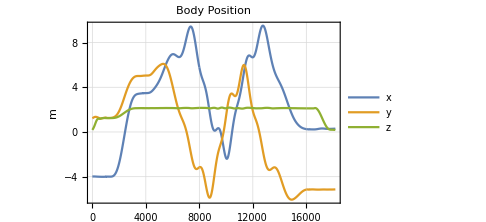
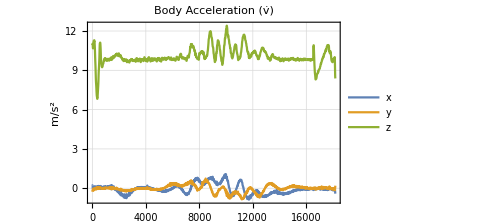
-Graphics- | -Graphics-

```mathematica
{{ListPlot[xᵀ,
PlotTheme->"Detailed",
Joined->True,
PlotLabel->"Body Position",
PlotLegends->{"x","y","z"},
PlotRange->All,
ImageSize->Medium,
FrameLabel->{None,"m"}],
ListPlot[vDotᵀ,
PlotTheme->"Detailed",
Joined->True,
PlotLabel->"Body Acceleration (v̇)",
PlotLegends->{"x","y","z"},
PlotRange->All,
ImageSize->Medium,
FrameLabel->{None,"m/s^2"}]}}//TableForm
```

From this we see that when the quad rotors body is stationary the recorded acceleration of the body is ~10m/s^2. Thus we note that the data labeled “acceleration body x”, “acceleration body y”, “acceleration body z” is actually a filtered fusion Vicon/IMU measurement. Thus we can modify our force fitting function:

F_B=m((v^·)_imu+ω_B×v_B)

Removing Coriolis from acceleration each time step:

```mathematica
𝕐=vDot+MapThread[#1×#2&,{ω,v}];
```

Here ŷ is the net forces applied on the quad rotor by the quad rotor as well as the aerodynamic forces on the quad rotor.

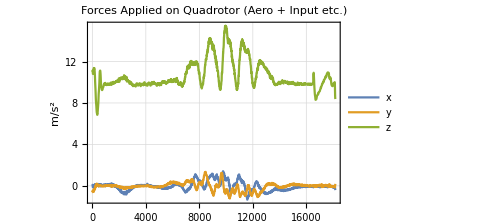

```mathematica
ListPlot[𝕐ᵀ,
PlotTheme->"Detailed",
Joined->True,
PlotLabel->"Forces Applied on Quadrotor (Aero + Input etc.)",
PlotLegends->{"x","y","z"},
PlotRange->All,
ImageSize->Medium,
FrameLabel->{None,"m/s^2"}]
```

Here we plot the motor speeds

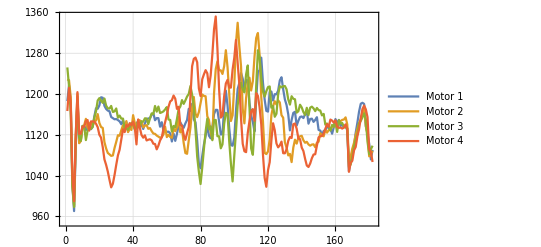

```mathematica
ListPlot[Ω⟦;;;;100⟧ᵀ,
PlotTheme->"Detailed",
Joined->True,
PlotLegends->{"Motor 1","Motor 2","Motor 3","Motor 4"}]
```

#### Fitting Force

As above we assume the forces on the quad rotor are a function of only the body linear and angular velocity, as well as the motor speeds.

x=(v_B ᵀ | ω_B ᵀ | Ω)ᵀ
F_B[x]:ℝ^10→ℝ^3

We are then going to be fitting 1/m

F_B=m((v^·)_imu+ω_B×v_B)

As  F_B is modeled as a quadratic we must apply the transform z=𝒻(x)=(𝟙
x
x⊗x). Constructing the set of sample points.

```mathematica
m=1.776;
𝕏=Join[v,ω,Ω,2];
𝒻=Module[{X},
X=Table[{Slot[i]},{i,Dimensions[𝕏]⟦2⟧}];
Evaluate[Squeeze[Join[{{1}},X,KroneckerProduct[X,X]]]]&];
ℤ=MapThread[𝒻,𝕏ᵀ];
```

Finally we can now compute the matrix 𝔻, 𝔼

```mathematica
𝕐=m*(vDot+MapThread[#1×#2&,{ω,v}]);
𝔻=Module[{n},
n=10;
(PseudoInverse[ℤ⟦;;;;n⟧].𝕐⟦;;;;n⟧)ᵀ
];
```

#### Measuring Goodness of Fit

We can then evaluate the performance of this model using

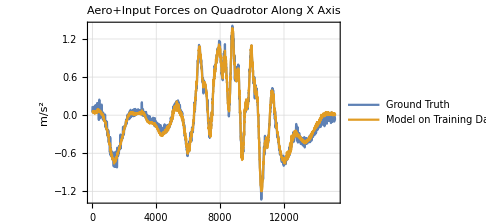
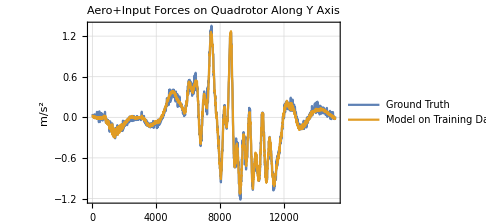
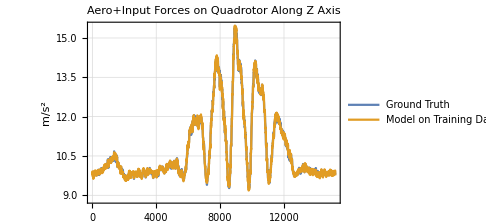
-Graphics- | -Graphics- | -Graphics-

```mathematica
Module[{groundTruth,trainingOutput,labels},
groundTruth=ŷ ᵀ;
trainingOutput=𝔻.ẑ ᵀ;
labels={"X","Y","Z"};
{Table[
ListPlot[{groundTruth⟦i⟧,trainingOutput⟦i⟧},PlotTheme->"Detailed",
Joined->True,
PlotLabel->"Aero+Input Forces on Quadrotor Along "<>labels⟦i⟧<>" Axis",
PlotLegends->Placed[{"Ground Truth","Model on Training Data"},Bottom],
PlotRange->All,
ImageSize->Medium,
FrameLabel->{None,"m/s^2"}]
,{i,3}]}
]//TableForm
```

Checking the goodness of fit using the coefficient of determination:

ȳ=1/N∑_(i=1)^N y_i
R^2=1-(∑_i Norm[y_i-f(x_i)])/(∑_i Norm[y_i-ȳ])

We compute the R^2 coefficient then:

```mathematica
Module[{𝕪,𝕗,N},
𝕪=Mean[ŷ];𝕗=(𝔻.ẑ ᵀ)ᵀ;N=Length[𝕗];
1-(∑_(i=1)^N Norm[ŷ⟦i⟧-𝕗⟦i⟧])/(∑_(i=1)^N Norm[ŷ⟦i⟧-𝕪])
]
```

0.934174639

#### Saving the quadratic least squares matrix:

```mathematica
Export[NotebookDirectory[]<>"/QuadraticLeastSquaresForces.mat",𝔻];
Module[{test},
test=Import[NotebookDirectory[]<>"/QuadraticLeastSquaresForces.mat"]⟦1⟧;
test==𝔻
]
```

True

### Torque Model

#### Fitting Force

As above we assume the forces on the quad rotor are a function of only the body linear and angular velocity, as well as the motor speeds.

x=(v_B ᵀ | ω_B ᵀ | Ωᵀ)ᵀ
(τ̂)_B[x]:ℝ^10→ℝ^3

(τ̂)_B=J(ω^·)_B+ω_B×J ω_B

As  F_B is modeled as a quadratic we must apply the transform z=𝒻(x)=(𝟙
x
x⊗x). Constructing the set of sample points.

```mathematica
J=({{0.01566089, 0.00000318037, 0.}, {0.00000318037, 0.01562078, 0.}, {0., 0., 0.02226868}});
𝕏=Join[v,ω,Ω,2];
𝒻=Module[{X},
X=Table[{Slot[i]},{i,Dimensions[𝕏]⟦2⟧}];
Evaluate[Squeeze[Join[{{1}},X,KroneckerProduct[X,X]]]]&];
ℤ=MapThread[𝒻,𝕏ᵀ];
```

Finally we can now compute the matrix 𝔻, 𝔼

```mathematica
𝕐=MapThread[J.#1+#2×(J.#2)&,{ωDot,ω}];
𝔼=Module[{n},
n=10;
(PseudoInverse[ℤ⟦;;;;n⟧].𝕐⟦;;;;n⟧)ᵀ
];
```

#### Measuring Goodness of Fit

We can then evaluate the performance of this model using

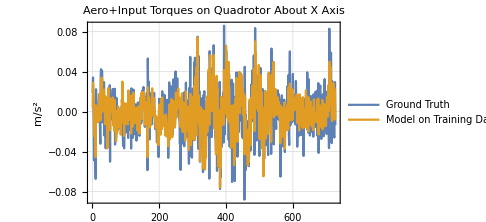
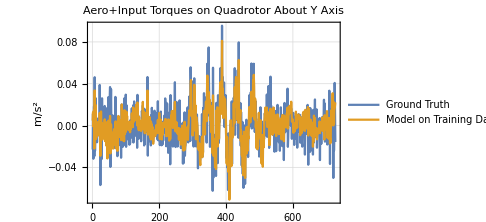
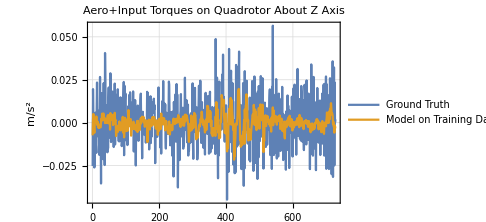
-Graphics- | -Graphics- | -Graphics-

```mathematica
Module[{groundTruth,trainingOutput,labels},
groundTruth=𝕐ᵀ;
trainingOutput=𝔼.ℤᵀ;
labels={"X","Y","Z"};
{Table[
ListPlot[{groundTruth⟦i,;;;;25⟧,trainingOutput⟦i,;;;;25⟧},PlotTheme->"Detailed",
Joined->True,
PlotLabel->"Aero+Input Torques on Quadrotor About "<>labels⟦i⟧<>" Axis",
PlotLegends->Placed[{"Ground Truth","Model on Training Data"},Bottom],
PlotRange->All,
ImageSize->Medium,
FrameLabel->{None,"m/s^2"}]
,{i,3}]}
]//TableForm
```

Checking the goodness of fit using the coefficient of determination:

ȳ=1/N∑_(i=1)^N y_i
R^2=1-(∑_i Norm[y_i-f(x_i)])/(∑_i Norm[y_i-ȳ])

We compute the R^2 coefficient then:

```mathematica
Module[{𝓎,τ,N},
𝓎=Mean[𝕐];τ=(𝔼.ℤᵀ)ᵀ;N=Length[τ];
1-(∑_(i=1)^N Norm[𝕐⟦i⟧-τ⟦i⟧])/(∑_(i=1)^N Norm[𝕐⟦i⟧-𝓎])
]
```

0.300259

#### Saving the quadratic least squares matrix:

```mathematica
Export[NotebookDirectory[]<>"/QuadraticLeastSquaresTorques.mat",𝔼];
Module[{test},
test=Import[NotebookDirectory[]<>"/QuadraticLeastSquaresTorques.mat"]⟦1⟧;
test==𝔼
]
```

True

## Testing Dataset 1

Loading in the testing data

```mathematica
testData=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-44-49_seg_1.csv"];
header=testData⟦1,;;⟧;testData1=testData⟦2;;,;;⟧;
testData2=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-44-49_seg_2.csv",HeaderLines->1];
testData3=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-44-49_seg_3.csv",HeaderLines->1];
testData4=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-44-49_seg_4.csv",HeaderLines->1];
testDataFull=Join[testData1,testData2,testData3,testData4,1];
testData=Join[testData2,testData3,1];
```

```mathematica
Module[{pos,downSample},
pos=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"pos x","pos y","pos z"}⟧;
downSample=Table[pos⟦n⟧,{n,1,Length[pos],20}];
Show[
ListPointPlot3D[downSample,PlotTheme->"Detailed",PlotRange->All]/.Point[a___]:>{Thick,Line[a]},
ListPointPlot3D[{First[pos]},PlotStyle->{Red,Large}],
ListPointPlot3D[{Last[pos]},PlotStyle->{Green,Large}]
]
]
```

-Graphics3D-

### Extracting Data

```mathematica
v̇=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"acc x","acc y","acc z"}⟧;
Ω=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"mot 1","mot 2","mot 3","mot 4"}⟧;Subscript[v, B]=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"vel x","vel y","vel z"}⟧;Subscript[ω, B]=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"ang vel x","ang vel y","ang vel z"}⟧;
q=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"quat w","quat x","quat y","quat z"}⟧;
```

Converting set of quaternions to a set of Rotation matrices

```mathematica
ℛ=2({{(#⟦1⟧)^2+(#⟦2⟧)^2-1/2, #⟦2⟧#⟦3⟧-#⟦1⟧#⟦4⟧, #⟦2⟧#⟦4⟧+#⟦1⟧#⟦3⟧}, {#⟦2⟧#⟦3⟧+#⟦1⟧#⟦4⟧, (#⟦1⟧)^2+(#⟦3⟧)^2-1/2, #⟦3⟧#⟦4⟧-#⟦1⟧#⟦2⟧}, {#⟦2⟧#⟦4⟧-#⟦1⟧#⟦3⟧, #⟦3⟧#⟦4⟧+#⟦1⟧#⟦2⟧, (#⟦1⟧)^2+(#⟦4⟧)^2-1/2}})&/@q;
```

Remove Coriolis terms

```mathematica
ȳ=v̇+MapThread[#1×#2&,{Subscript[ω, B],Subscript[v, B]}];
x̄=Join[Subscript[v, B],Subscript[ω, B],Ω,2];
```

Redefining quadratic map

```mathematica
X=Table[{Slot[i]},{i,Dimensions[x̂]⟦2⟧}];
𝒻=Evaluate[Squeeze[Join[{{1}},X,KroneckerProduct[X,X]]]]&;
z̄=MapThread[𝒻,x̄ ᵀ];
```

We can now compute the output on the testing dataset

```mathematica
𝔻.z̄ ᵀ
```

{{0.44979927637,0.44407629383,0.43446259963,0.41876307463,17912,-0.02649488101,-0.02196961515,-0.01660825423,-0.01039499508},{1},{1}}
 |  |  |  |

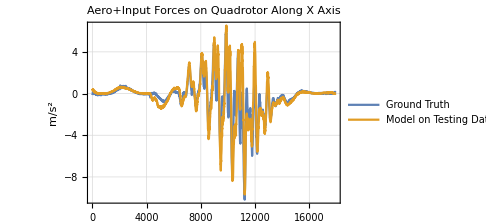
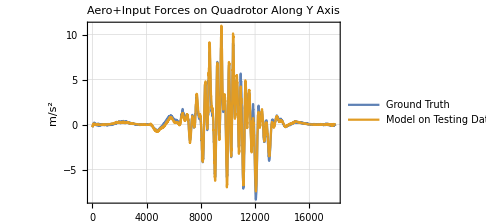
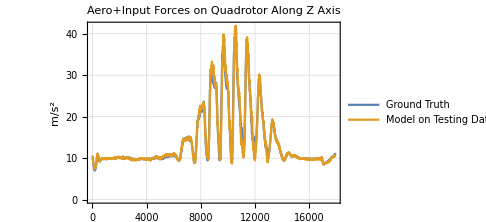
-Graphics- | -Graphics- | -Graphics-

```mathematica
Module[{groundTruth,testingOutput,labels},
groundTruth=ȳ ᵀ;
testingOutput=𝔻.z̄ ᵀ;
labels={"X","Y","Z"};
{Table[
ListPlot[{groundTruth⟦i⟧,testingOutput⟦i⟧},
PlotTheme->"Detailed",
Joined->True,
PlotLabel->"Aero+Input Forces on Quadrotor Along "<>labels⟦i⟧<>" Axis",
PlotLegends->Placed[{"Ground Truth","Model on Testing Data"},Bottom],
PlotRange->All,
ImageSize->Medium,
FrameLabel->{None,"m/s^2"}]
,{i,3}]}
]//TableForm
```

#### Test data Goodness of Fit

```mathematica
Module[{𝕪,𝕗,N},
𝕪=Mean[ȳ];𝕗=(𝔻.z̄ ᵀ)ᵀ;N=Length[𝕗];
1-(∑_(i=1)^N Norm[ȳ⟦i⟧-𝕗⟦i⟧])/(∑_(i=1)^N Norm[ȳ⟦i⟧-𝕪])
]
```

0.8572201622

## Testing Dataset 2

Loading in the testing data

```mathematica
testData=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-54-06_seg_1.csv"];
header=testData⟦1,;;⟧;testData1=testData⟦2;;,;;⟧;
testData2=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-54-06_seg_2.csv",HeaderLines->1];
testData3=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-54-06_seg_3.csv",HeaderLines->1];
testData4=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-54-06_seg_4.csv",HeaderLines->1];
testDataFull=Join[testData1,testData2,testData3,testData4,1];
```

```mathematica
Module[{pos,downSample},
pos=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"pos x","pos y","pos z"}⟧;
downSample=Table[pos⟦n⟧,{n,1,Length[pos],20}];
Show[
ListPointPlot3D[downSample,PlotTheme->"Detailed",PlotRange->All]/.Point[a___]:>{Thick,Line[a]},
ListPointPlot3D[{First[pos]},PlotStyle->{Red,Large}],
ListPointPlot3D[{Last[pos]},PlotStyle->{Green,Large}]
]
]
```

-Graphics3D-

### Extracting Data

```mathematica
v̇=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"acc x","acc y","acc z"}⟧;
Ω=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"mot 1","mot 2","mot 3","mot 4"}⟧;Subscript[v, B]=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"vel x","vel y","vel z"}⟧;Subscript[ω, B]=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"ang vel x","ang vel y","ang vel z"}⟧;
q=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"quat w","quat x","quat y","quat z"}⟧;
```

Converting set of quaternions to a set of Rotation matrices

```mathematica
ℛ=2({{(#⟦1⟧)^2+(#⟦2⟧)^2-1/2, #⟦2⟧#⟦3⟧-#⟦1⟧#⟦4⟧, #⟦2⟧#⟦4⟧+#⟦1⟧#⟦3⟧}, {#⟦2⟧#⟦3⟧+#⟦1⟧#⟦4⟧, (#⟦1⟧)^2+(#⟦3⟧)^2-1/2, #⟦3⟧#⟦4⟧-#⟦1⟧#⟦2⟧}, {#⟦2⟧#⟦4⟧-#⟦1⟧#⟦3⟧, #⟦3⟧#⟦4⟧+#⟦1⟧#⟦2⟧, (#⟦1⟧)^2+(#⟦4⟧)^2-1/2}})&/@q;
```

Remove Coriolis terms

```mathematica
ȳ=v̇+MapThread[#1×#2&,{Subscript[ω, B],Subscript[v, B]}];
x̄=Join[Subscript[v, B],Subscript[ω, B],Ω,2];
```

Redefining quadratic map

```mathematica
X=Table[{Slot[i]},{i,Dimensions[x̂]⟦2⟧}];
𝒻=Evaluate[Squeeze[Join[{{1}},X,KroneckerProduct[X,X]]]]&;
z̄=MapThread[𝒻,x̄ ᵀ];
```

We can now compute the output on the testing dataset

```mathematica
𝔻.z̄ ᵀ
```

{{0.26005694964,0.26663299082,0.27350798994,0.28007762645,17951,0.02676023606,0.02564769438,0.0246155007,0.02365628898},{1},{1}}
 |  |  |  |

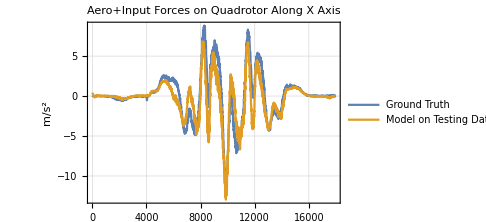
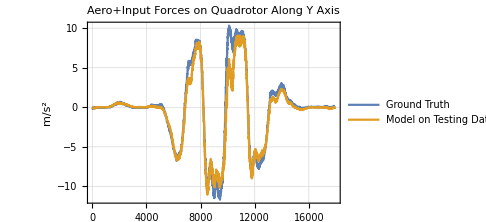
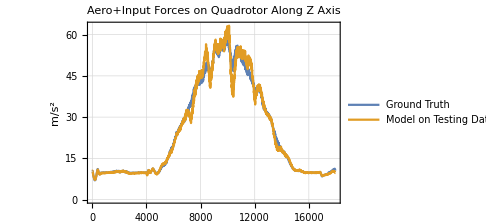
-Graphics- | -Graphics- | -Graphics-

```mathematica
Module[{groundTruth,testingOutput,labels},
groundTruth=ȳ ᵀ;
testingOutput=𝔻.z̄ ᵀ;
labels={"X","Y","Z"};
{Table[
ListPlot[{groundTruth⟦i⟧,testingOutput⟦i⟧},
PlotTheme->"Detailed",
Joined->True,
PlotLabel->"Aero+Input Forces on Quadrotor Along "<>labels⟦i⟧<>" Axis",
PlotLegends->Placed[{"Ground Truth","Model on Testing Data"},Bottom],
PlotRange->All,
ImageSize->Medium,
FrameLabel->{None,"m/s^2"}]
,{i,3}]}
]//TableForm
```

#### Test data Goodness of Fit

```mathematica
Module[{𝕪,𝕗,N},
𝕪=Mean[ȳ];𝕗=(𝔻.z̄ ᵀ)ᵀ;N=Length[𝕗];
1-(∑_(i=1)^N Norm[ȳ⟦i⟧-𝕗⟦i⟧])/(∑_(i=1)^N Norm[ȳ⟦i⟧-𝕪])
]
```

0.8988434507

## Testing Dataset 3

Loading in the testing data

```mathematica
testData=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-16-10-37_seg_1.csv"];
header=testData⟦1,;;⟧;testData1=testData⟦2;;,;;⟧;
testData2=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-16-10-37_seg_2.csv",HeaderLines->1];
testData3=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-16-10-37_seg_3.csv",HeaderLines->1];
testData4=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-16-10-37_seg_4.csv",HeaderLines->1];
testDataFull=Join[testData1,testData2,testData3,testData4,1];
testData=Join[testData2,testData3,1];
```

```mathematica
Module[{pos,downSample},
pos=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"pos x","pos y","pos z"}⟧;
downSample=Table[pos⟦n⟧,{n,1,Length[pos],100}];
Show[
ListPointPlot3D[downSample,PlotTheme->"Detailed",PlotRange->All]/.Point[a___]:>{Thick,Line[a]},
ListPointPlot3D[{First[pos]},PlotStyle->{Red,Large}],
ListPointPlot3D[{Last[pos]},PlotStyle->{Green,Large}]
]
]
```

-Graphics3D-

### Extracting Data

```mathematica
v̇=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"acc x","acc y","acc z"}⟧;
Ω=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"mot 1","mot 2","mot 3","mot 4"}⟧;Subscript[v, B]=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"vel x","vel y","vel z"}⟧;Subscript[ω, B]=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"ang vel x","ang vel y","ang vel z"}⟧;
q=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"quat w","quat x","quat y","quat z"}⟧;
```

Converting set of quaternions to a set of Rotation matrices

```mathematica
ℛ=2({{(#⟦1⟧)^2+(#⟦2⟧)^2-1/2, #⟦2⟧#⟦3⟧-#⟦1⟧#⟦4⟧, #⟦2⟧#⟦4⟧+#⟦1⟧#⟦3⟧}, {#⟦2⟧#⟦3⟧+#⟦1⟧#⟦4⟧, (#⟦1⟧)^2+(#⟦3⟧)^2-1/2, #⟦3⟧#⟦4⟧-#⟦1⟧#⟦2⟧}, {#⟦2⟧#⟦4⟧-#⟦1⟧#⟦3⟧, #⟦3⟧#⟦4⟧+#⟦1⟧#⟦2⟧, (#⟦1⟧)^2+(#⟦4⟧)^2-1/2}})&/@q;
```

Remove Coriolis terms

```mathematica
ȳ=v̇+MapThread[#1×#2&,{Subscript[ω, B],Subscript[v, B]}];
x̄=Join[Subscript[v, B],Subscript[ω, B],Ω,2];
```

Redefining quadratic map

```mathematica
X=Table[{Slot[i]},{i,Dimensions[x̂]⟦2⟧}];
𝒻=Evaluate[Squeeze[Join[{{1}},X,KroneckerProduct[X,X]]]]&;
z̄=MapThread[𝒻,x̄ ᵀ];
```

We can now compute the output on the testing dataset

```mathematica
𝔻.z̄ ᵀ
```

{{-0.05407588607,-0.04497008844,-0.03303533183,-0.02282731245,17446,-0.11793221413,-0.117889819,-0.11562689847,-0.11155714104},{1},{1}}
 |  |  |  |

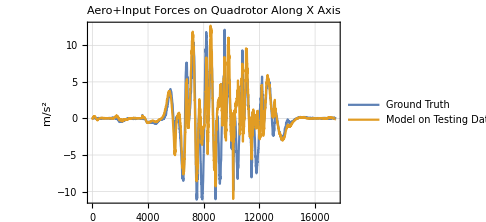
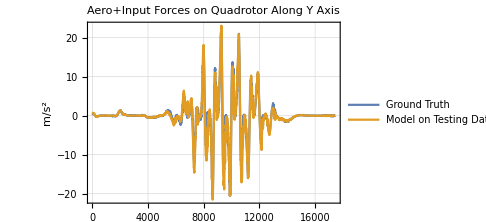
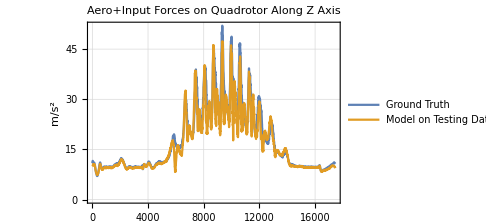
-Graphics- | -Graphics- | -Graphics-

```mathematica
Module[{groundTruth,testingOutput,labels},
groundTruth=ȳ ᵀ;
testingOutput=𝔻.z̄ ᵀ;
labels={"X","Y","Z"};
{Table[
ListPlot[{groundTruth⟦i⟧,testingOutput⟦i⟧},
PlotTheme->"Detailed",
Joined->True,
PlotLabel->"Aero+Input Forces on Quadrotor Along "<>labels⟦i⟧<>" Axis",
PlotLegends->Placed[{"Ground Truth","Model on Testing Data"},Bottom],
PlotRange->All,
ImageSize->Medium,
FrameLabel->{None,"m/s^2"}]
,{i,3}]}
]//TableForm
```

#### Test data Goodness of Fit

```mathematica
Module[{𝕪,𝕗,N},
𝕪=Mean[ȳ];𝕗=(𝔻.z̄ ᵀ)ᵀ;N=Length[𝕗];
1-(∑_(i=1)^N Norm[ȳ⟦i⟧-𝕗⟦i⟧])/(∑_(i=1)^N Norm[ȳ⟦i⟧-𝕪])
]
```

0.7523526093

From the graph of the dataset we can see this trajectory repeatedly drives the quad rotor through its own prop wash which the model is unable to account for. F_B is not a function of the surrounding air velocity.

## Testing Dataset 4

Loading in the testing data

```mathematica
testData=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-16-12-22_seg_1.csv"];
header=testData⟦1,;;⟧;testData1=testData⟦2;;,;;⟧;
testData2=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-16-12-22_seg_2.csv",HeaderLines->1];
testData3=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-16-12-22_seg_3.csv",HeaderLines->1];
testData4=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-16-12-22_seg_4.csv",HeaderLines->1];
testDataFull=Join[testData1,testData2,testData3,testData4,1];
testData=Join[testData2,testData3,1];
```

```mathematica
Module[{pos,downSample},
pos=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"pos x","pos y","pos z"}⟧;
downSample=Table[pos⟦n⟧,{n,1,Length[pos],100}];
Show[
ListPointPlot3D[downSample,PlotTheme->"Detailed",PlotRange->All]/.Point[a___]:>{Thick,Line[a]},
ListPointPlot3D[{First[pos]},PlotStyle->{Red,Large}],
ListPointPlot3D[{Last[pos]},PlotStyle->{Green,Large}]
]
]
```

-Graphics3D-

### Extracting Data

```mathematica
v̇=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"acc x","acc y","acc z"}⟧;
Ω=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"mot 1","mot 2","mot 3","mot 4"}⟧;Subscript[v, B]=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"vel x","vel y","vel z"}⟧;Subscript[ω, B]=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"ang vel x","ang vel y","ang vel z"}⟧;
q=testDataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"quat w","quat x","quat y","quat z"}⟧;
```

Converting set of quaternions to a set of Rotation matrices

```mathematica
ℛ=2({{(#⟦1⟧)^2+(#⟦2⟧)^2-1/2, #⟦2⟧#⟦3⟧-#⟦1⟧#⟦4⟧, #⟦2⟧#⟦4⟧+#⟦1⟧#⟦3⟧}, {#⟦2⟧#⟦3⟧+#⟦1⟧#⟦4⟧, (#⟦1⟧)^2+(#⟦3⟧)^2-1/2, #⟦3⟧#⟦4⟧-#⟦1⟧#⟦2⟧}, {#⟦2⟧#⟦4⟧-#⟦1⟧#⟦3⟧, #⟦3⟧#⟦4⟧+#⟦1⟧#⟦2⟧, (#⟦1⟧)^2+(#⟦4⟧)^2-1/2}})&/@q;
```

Remove Coriolis terms

```mathematica
ȳ=v̇+MapThread[#1×#2&,{Subscript[ω, B],Subscript[v, B]}];
x̄=Join[Subscript[v, B],Subscript[ω, B],Ω,2];
```

Redefining quadratic map

```mathematica
X=Table[{Slot[i]},{i,Dimensions[x̂]⟦2⟧}];
𝒻=Evaluate[Squeeze[Join[{{1}},X,KroneckerProduct[X,X]]]]&;
z̄=MapThread[𝒻,x̄ ᵀ];
```

We can now compute the output on the testing dataset

```mathematica
𝔻.z̄ ᵀ
```

{{0.27246809979,0.27790872335,0.27952753191,0.27784318321,17484,0.05273589172,0.05381564339,0.05491314561,0.055857425713},{1},{1}}
 |  |  |  |

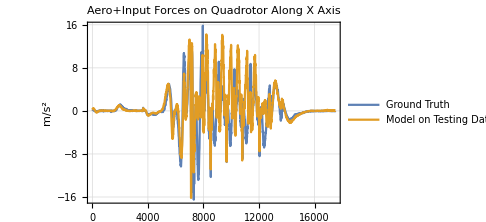
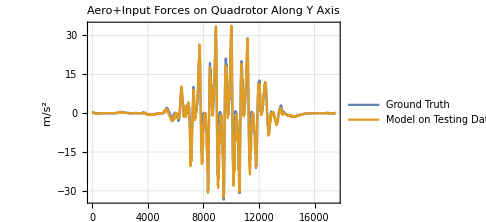
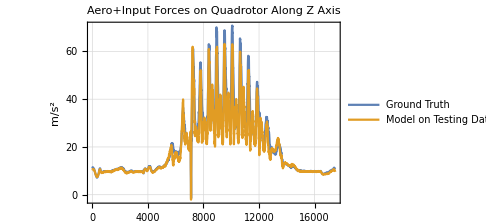
-Graphics- | -Graphics- | -Graphics-

```mathematica
Module[{groundTruth,testingOutput,labels},
groundTruth=ȳ ᵀ;
testingOutput=𝔻.z̄ ᵀ;
labels={"X","Y","Z"};
{Table[
ListPlot[{groundTruth⟦i⟧,testingOutput⟦i⟧},
PlotTheme->"Detailed",
Joined->True,
PlotLabel->"Aero+Input Forces on Quadrotor Along "<>labels⟦i⟧<>" Axis",
PlotLegends->Placed[{"Ground Truth","Model on Testing Data"},Bottom],
PlotRange->All,
ImageSize->Medium,
FrameLabel->{None,"m/s^2"}]
,{i,3}]}
]//TableForm
```

#### Test data Goodness of Fit

```mathematica
Module[{𝕪,𝕗,N},
𝕪=Mean[ȳ];𝕗=(𝔻.z̄ ᵀ)ᵀ;N=Length[𝕗];
1-(∑_(i=1)^N Norm[ȳ⟦i⟧-𝕗⟦i⟧])/(∑_(i=1)^N Norm[ȳ⟦i⟧-𝕪])
]
```

0.7324512078

From the graph of the dataset we can see this trajectory repeatedly drives the quad rotor through its own prop wash which the model is unable to account for. F_B is not a function of the surrounding air velocity.